#### Potencial que tem os autoestados dos 3 pares quark-antiquark https://community.wolfram.com/groups/-/m/t/3311726

```mathematica
ClearAll["Global`*"]
```

```mathematica
Dados={13.8,18.8,199.2,2559.2,8369.2,18.8,23.8,204.2,2564.2,8374.2,199.2,204.2,384.6,2744.6,8554.6,2559.2,2564.2,2744.6,5104.6,10914.6,8369.2,8374.2,8554.6,10914.6,
16724.6,18.8,23.8,204.2,2564.2,8374.2,23.8,28.8,209.2,2569.2,8379.2,204.2,209.2,389.6,2749.6,8559.6,2564.2,2569.2,2749.6,5109.6,10919.6,8374.2,8379.2,8559.6,10919.6,16729.6,199.2,204.2,384.6,2744.6,8554.6,204.2,209.2,389.6,2749.6,8559.6,384.6,389.6,570.0,2930.0,8740.0,2744.6,2749.6,2930.0,5290.0,11100.0,8554.6,8559.6,8740.0,11100.0,16910.0,2559.2,2564.2,2744.6,5104.6,10914.6,2564.2,2569.2,2749.6,5109.6,10919.6,2744.6,2749.6,2930.0,5290.0,11100.0,5104.6,5109.6,5290.0,7650.0,13460.0,10914.6,10919.6,11100.0,13460.0,19270.0,8369.2,8374.2,8554.6,10914.6,16724.6,8374.2,8379.2,8559.6,10919.6,16729.6,8554.6,8559.6,8740.0,11100.0,16910.0,10914.6,10919.6,11100.0,13460.0,19270.0,16724.6,16729.6,16910.0,19270.0,25080.0}
```

{13.8,18.8,199.2,2559.2,8369.2,18.8,23.8,204.2,2564.2,8374.2,199.2,204.2,384.6,2744.6,8554.6,2559.2,2564.2,2744.6,5104.6,10914.6,8369.2,8374.2,8554.6,10914.6,16724.6,18.8,23.8,204.2,2564.2,8374.2,23.8,28.8,209.2,2569.2,8379.2,204.2,209.2,389.6,2749.6,8559.6,2564.2,2569.2,2749.6,5109.6,10919.6,8374.2,8379.2,8559.6,10919.6,16729.6,199.2,204.2,384.6,2744.6,8554.6,204.2,209.2,389.6,2749.6,8559.6,384.6,389.6,570.,2930.,8740.,2744.6,2749.6,2930.,5290.,11100.,8554.6,8559.6,8740.,11100.,16910.,2559.2,2564.2,2744.6,5104.6,10914.6,2564.2,2569.2,2749.6,5109.6,10919.6,2744.6,2749.6,2930.,5290.,11100.,5104.6,5109.6,5290.,7650.,13460.,10914.6,10919.6,11100.,13460.,19270.,8369.2,8374.2,8554.6,10914.6,16724.6,8374.2,8379.2,8559.6,10919.6,16729.6,8554.6,8559.6,8740.,11100.,16910.,10914.6,10919.6,11100.,13460.,19270.,16724.6,16729.6,16910.,19270.,25080.}

```mathematica
BarDat=Partition[Dados,5]
```

{{13.8,18.8,199.2,2559.2,8369.2},{18.8,23.8,204.2,2564.2,8374.2},{199.2,204.2,384.6,2744.6,8554.6},{2559.2,2564.2,2744.6,5104.6,10914.6},{8369.2,8374.2,8554.6,10914.6,16724.6},{18.8,23.8,204.2,2564.2,8374.2},{23.8,28.8,209.2,2569.2,8379.2},{204.2,209.2,389.6,2749.6,8559.6},{2564.2,2569.2,2749.6,5109.6,10919.6},{8374.2,8379.2,8559.6,10919.6,16729.6},{199.2,204.2,384.6,2744.6,8554.6},{204.2,209.2,389.6,2749.6,8559.6},{384.6,389.6,570.,2930.,8740.},{2744.6,2749.6,2930.,5290.,11100.},{8554.6,8559.6,8740.,11100.,16910.},{2559.2,2564.2,2744.6,5104.6,10914.6},{2564.2,2569.2,2749.6,5109.6,10919.6},{2744.6,2749.6,2930.,5290.,11100.},{5104.6,5109.6,5290.,7650.,13460.},{10914.6,10919.6,11100.,13460.,19270.},{8369.2,8374.2,8554.6,10914.6,16724.6},{8374.2,8379.2,8559.6,10919.6,16729.6},{8554.6,8559.6,8740.,11100.,16910.},{10914.6,10919.6,11100.,13460.,19270.},{16724.6,16729.6,16910.,19270.,25080.}}

```mathematica
BarDat[[1]]
```

{13.8,18.8,199.2,2559.2,8369.2}

```mathematica
BarDat[[1,5]]
```

8369.2

```mathematica
BarTit={"uu","ud","us","uc","ub","du","dd","ds","dc","db","su","sd","ss","sc","sb","cu","cd","cs","cc","cb","bu","bd","bs","bc","bb"}
```

{uu,ud,us,uc,ub,du,dd,ds,dc,db,su,sd,ss,sc,sb,cu,cd,cs,cc,cb,bu,bd,bs,bc,bb}

```mathematica
PotxMax=20.0;
xmax=0.5;
NumRegArq=500;
xstep=(2.0*xmax)/NumRegArq;
PorcCorte=0.95;
ListaCorte={};
```

```mathematica
dressingTransformationPotentials[evals_,xMax_,opts___]:=Module[{ε,f,g,evals1=Sort[evals]-Max[evals],W=0&},Do[ε=evals1[[-k]];
W=NDSolveValue[{f'[x]-f[x]^2+W[x]==ε,f[0]==0,g'[x]==4 f[x] f'[x]-W'[x],g[0]==2 ε-W[0]},{f,g},{x,0,xMax},opts][[2]],{k,2,Length[evals1]}];
Function@@{ξ,W[ξ]+Max[evals]}]
```

#### Loop varredura dos 5 barions

```mathematica
matout=OpenWrite["ResHEP1.csv"];
```

==========   Barion: uu==========

Raio do poco para PotCorte=7950.74 xCorte=0.12

Potencial obtido:

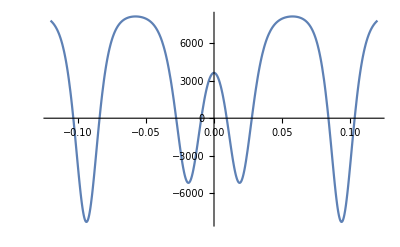

Niveis experimentais:

{13.8,18.8,199.2,2559.2,8369.2}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{0,«16000»,64001},«1»},{0.000666667,-0.000166667,0.000333333,-0.000166667,0.00133333,-0.000166667,«63989»,0.000333333,0.000333333,0.00266667,0.000333333,0.000333333,0.00266667}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{14.4993,19.5153,199.503,2559.63,8370.33}

==========   Barion: ud==========

Raio do poco para PotCorte=7955.49 xCorte=0.12

Potencial obtido:

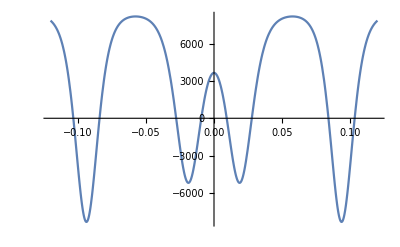

Niveis experimentais:

{18.8,23.8,204.2,2564.2,8374.2}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{0,«16000»,64001},«1»},{0.000666667,-0.000166667,0.000333333,-0.000166667,0.00133333,-0.000166667,«63989»,0.000333333,0.000333333,0.00266667,0.000333333,0.000333333,0.00266667}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{19.4993,24.5153,204.503,2564.63,8375.33}

==========   Barion: us==========

Raio do poco para PotCorte=8126.87 xCorte=0.12

Potencial obtido:

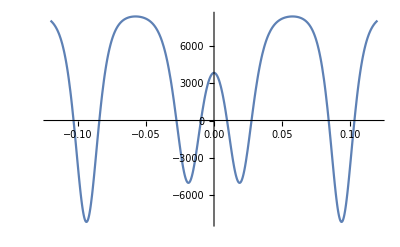

Niveis experimentais:

{199.2,204.2,384.6,2744.6,8554.6}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

General::stop: Further output of Eigensystem::maxit2 will be suppressed during this calculation.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«2»,{1,{{0,«16000»,64001},«1»},{0.000666667,-0.000166667,0.000333333,-0.000166667,0.00133333,-0.000166667,«63989»,0.000333333,0.000333333,0.00266667,0.000333333,0.000333333,0.00266667}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

General::stop: Further output of Eigensystem::chnpdef will be suppressed during this calculation.

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{199.897,204.914,384.903,2745.03,8555.75}

==========   Barion: uc==========

Raio do poco para PotCorte=10368.9 xCorte=0.118

Potencial obtido:

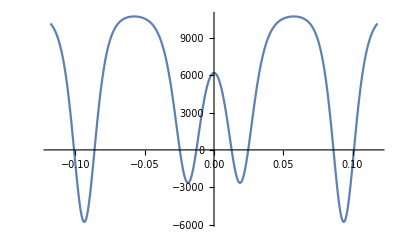

Niveis experimentais:

{2559.2,2564.2,2744.6,5104.6,10914.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{2559.9,2564.91,2744.9,5105.03,10916.}

==========   Barion: ub==========

Raio do poco para PotCorte=15888.4 xCorte=0.116

Potencial obtido:

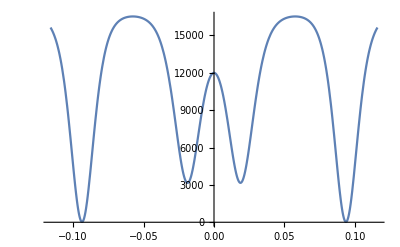

Niveis experimentais:

{8369.2,8374.2,8554.6,10914.6,16724.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{8369.9,8374.92,8554.9,10915.,16726.3}

==========   Barion: du==========

Raio do poco para PotCorte=7955.49 xCorte=0.12

Potencial obtido:

-Graphics-

Niveis experimentais:

{18.8,23.8,204.2,2564.2,8374.2}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{19.4993,24.5153,204.503,2564.63,8375.33}

==========   Barion: dd==========

Raio do poco para PotCorte=7960.24 xCorte=0.12

Potencial obtido:

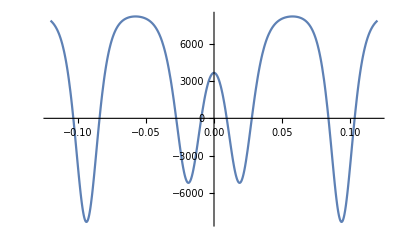

Niveis experimentais:

{23.8,28.8,209.2,2569.2,8379.2}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{24.4993,29.5153,209.503,2569.63,8380.33}

==========   Barion: ds==========

Raio do poco para PotCorte=8131.62 xCorte=0.12

Potencial obtido:

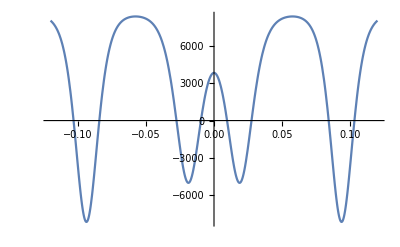

Niveis experimentais:

{204.2,209.2,389.6,2749.6,8559.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{204.897,209.914,389.903,2750.03,8560.75}

==========   Barion: dc==========

Raio do poco para PotCorte=10373.6 xCorte=0.118

Potencial obtido:

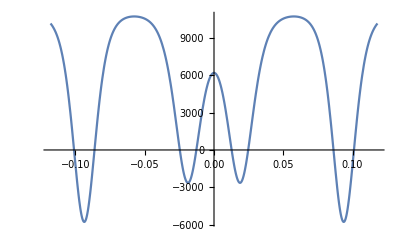

Niveis experimentais:

{2564.2,2569.2,2749.6,5109.6,10919.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{2564.9,2569.91,2749.9,5110.03,10921.}

==========   Barion: db==========

Raio do poco para PotCorte=15893.1 xCorte=0.116

Potencial obtido:

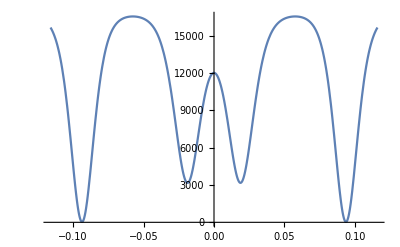

Niveis experimentais:

{8374.2,8379.2,8559.6,10919.6,16729.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{8374.9,8379.92,8559.9,10920.,16731.3}

==========   Barion: su==========

Raio do poco para PotCorte=8126.87 xCorte=0.12

Potencial obtido:

-Graphics-

Niveis experimentais:

{199.2,204.2,384.6,2744.6,8554.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{199.897,204.914,384.903,2745.03,8555.75}

==========   Barion: sd==========

Raio do poco para PotCorte=8131.62 xCorte=0.12

Potencial obtido:

-Graphics-

Niveis experimentais:

{204.2,209.2,389.6,2749.6,8559.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{204.897,209.914,389.903,2750.03,8560.75}

==========   Barion: ss==========

Raio do poco para PotCorte=8303. xCorte=0.12

Potencial obtido:

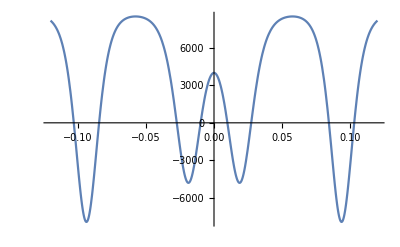

Niveis experimentais:

{384.6,389.6,570.,2930.,8740.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{385.297,390.314,570.303,2930.43,8741.17}

==========   Barion: sc==========

Raio do poco para PotCorte=10545. xCorte=0.118

Potencial obtido:

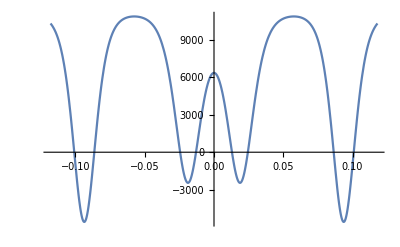

Niveis experimentais:

{2744.6,2749.6,2930.,5290.,11100.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{2745.3,2750.31,2930.3,5290.43,11101.4}

==========   Barion: sb==========

Raio do poco para PotCorte=16064.5 xCorte=0.116

Potencial obtido:

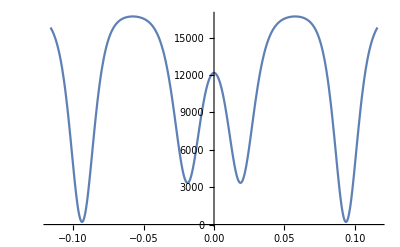

Niveis experimentais:

{8554.6,8559.6,8740.,11100.,16910.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{8555.3,8560.31,8740.3,11100.4,16911.7}

==========   Barion: cu==========

Raio do poco para PotCorte=10368.9 xCorte=0.118

Potencial obtido:

-Graphics-

Niveis experimentais:

{2559.2,2564.2,2744.6,5104.6,10914.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{2559.9,2564.91,2744.9,5105.03,10916.}

==========   Barion: cd==========

Raio do poco para PotCorte=10373.6 xCorte=0.118

Potencial obtido:

-Graphics-

Niveis experimentais:

{2564.2,2569.2,2749.6,5109.6,10919.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{2564.9,2569.91,2749.9,5110.03,10921.}

==========   Barion: cs==========

Raio do poco para PotCorte=10545. xCorte=0.118

Potencial obtido:

-Graphics-

Niveis experimentais:

{2744.6,2749.6,2930.,5290.,11100.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{2745.3,2750.31,2930.3,5290.43,11101.4}

==========   Barion: cc==========

Raio do poco para PotCorte=12787. xCorte=0.118

Potencial obtido:

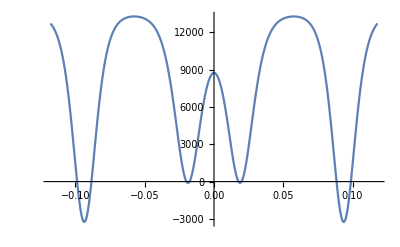

Niveis experimentais:

{5104.6,5109.6,5290.,7650.,13460.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{5105.3,5110.31,5290.3,7650.43,13461.5}

==========   Barion: cb==========

Raio do poco para PotCorte=18306.5 xCorte=0.116

Potencial obtido:

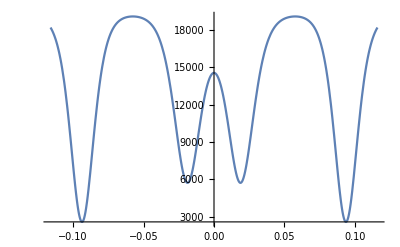

Niveis experimentais:

{10914.6,10919.6,11100.,13460.,19270.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{10915.3,10920.3,11100.3,13460.4,19271.9}

==========   Barion: bu==========

Raio do poco para PotCorte=15888.4 xCorte=0.116

Potencial obtido:

-Graphics-

Niveis experimentais:

{8369.2,8374.2,8554.6,10914.6,16724.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{8369.9,8374.92,8554.9,10915.,16726.3}

==========   Barion: bd==========

Raio do poco para PotCorte=15893.1 xCorte=0.116

Potencial obtido:

-Graphics-

Niveis experimentais:

{8374.2,8379.2,8559.6,10919.6,16729.6}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{8374.9,8379.92,8559.9,10920.,16731.3}

==========   Barion: bs==========

Raio do poco para PotCorte=16064.5 xCorte=0.116

Potencial obtido:

-Graphics-

Niveis experimentais:

{8554.6,8559.6,8740.,11100.,16910.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{8555.3,8560.31,8740.3,11100.4,16911.7}

==========   Barion: bc==========

Raio do poco para PotCorte=18306.5 xCorte=0.116

Potencial obtido:

-Graphics-

Niveis experimentais:

{10914.6,10919.6,11100.,13460.,19270.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{10915.3,10920.3,11100.3,13460.4,19271.9}

==========   Barion: bb==========

Raio do poco para PotCorte=23826. xCorte=0.114

Potencial obtido:

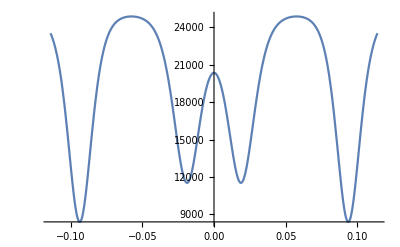

Niveis experimentais:

{16724.6,16729.6,16910.,19270.,25080.}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{16725.3,16730.3,16910.3,19270.4,25082.2}

ResHEP1.csv

```mathematica
NivCalc=5;
For[ii=1,ii≤Length[BarDat],ii++,
NivElem=BarDat[[ii]];
PotCorte=Evaluate[PorcCorte*NivElem[[NivCalc]]];

Print["==========   Barion: ",BarTit[[ii]],"=========="];
V=dressingTransformationPotentials[NivElem,PotxMax];
xCorte=PotxMax;
While [(xCorte>0.0)&&(PotCorte<V[xCorte]),xCorte=xCorte-xstep];
Print["Raio do poco para PotCorte=",PotCorte," xCorte=",xCorte];
Print["Potencial obtido:"];
Print[Plot[V[Abs[x]],{x,-xCorte,xCorte},PlotRange->All]];
Print["Niveis experimentais:"];
Print[NivElem];
ndse=NDEigensystem[-ψ''[x]+V[Abs[x]] ψ[x],ψ,{x,-PotxMax,PotxMax},NivCalc,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.005}}}}];
Print["Niveis obtidos pela solucao eq Schrodinger com este potencial:"];
Print[ndse[[1]]];
WriteString[matout,"\n===== Barion ",BarTit[[ii]]," =====; \n"];
WriteString[matout,"Energia=; ",ToString[BarDat[[ii,5]],InputForm],"; \n"];
WriteString[matout,"xCorte=; ",ToString[xCorte,InputForm],"; \n\n"];
lista={"x; Pot; "};
For[i=1,i<=NivCalc,i++,lista=Append[lista,StringJoin["Psi",ToString[i,InputForm],"; "]]];
lista=Append[lista,"\n"];
Cabec=StringJoin[lista];
WriteString[matout,Cabec];
Do[
lista={};
lista=Append[lista,StringJoin[ToString[x,InputForm],"; ",ToString[V[Abs[x]],InputForm],"; "]];
For[i=1,i<=NivCalc,i++,lista=Append[lista,StringJoin[StringJoin[ToString[ndse[[2,i]][x],InputForm],"; "]]]];
lista=Append[lista,"\n"];
Cabec=StringJoin[lista];
WriteString[matout,Cabec],{x,-xCorte,xCorte,xCorte/NumRegArq}];

]
Close[matout]
```